## RegularPolygon-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (10-Nov-2012)) loaded Sat 10 Nov 2012 15:50:27
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
p=RegularPolygon[7]
```

{{1.,0.},{0.62349,0.781831},{-0.222521,0.974928},{-0.900969,0.433884},{-0.900969,-0.433884},{-0.222521,-0.974928},{0.62349,-0.781831}}

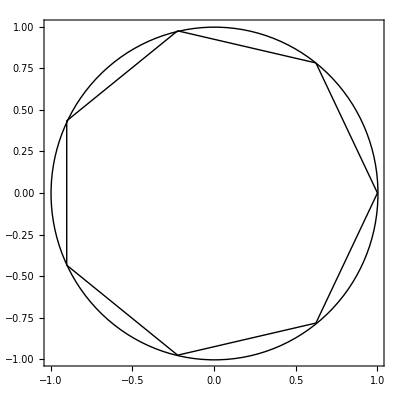

```mathematica
Show[Boundary[p],Graphics[Circle[{0,0}, 1]],  Frame-> True]
```

```mathematica
q=RegularPolygon[7, Pi/2, 2, -1, 3Pi/4]
```

{{1.41421,-1.41421},{1.43459,-0.328909},{0.374686,1.00407},{-0.96736,1.58096},{-1.58096,0.96736},{-1.00407,-0.374686},{0.328909,-1.43459}}

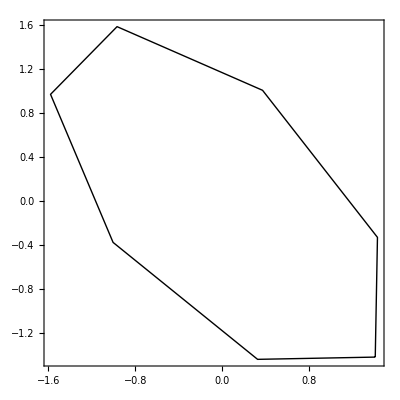

```mathematica
Show[Boundary[q], Frame-> True]
```

```mathematica
r=RegularPolygon[7, Pi/2, 2, .5, 3Pi/4]
```

{{1.11691,-1.6375},{1.62326,-0.844834},{0.192669,1.45296},{-0.998623,2.07237},{-1.78608,0.473224},{-1.38235,-0.209726},{0.501032,-0.915142}}

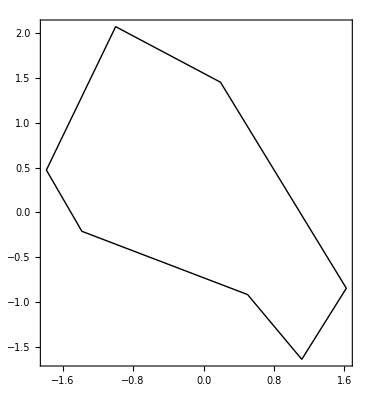

```mathematica
Show[Boundary[r], Frame-> True]
```